```mathematica
Manipulate[Limit[Sin[a*x]/Sin[b*x],x->0],{a,1,5},{b,2,3}]
```

```mathematica
Limit[x^(x^x-1),x->0]
```

1

```mathematica
Series[x/(ⅇ^x-1),{x,0,10}]
```

1-x/2+x^2/12-x^4/720+x^6/30240-x^8/1209600+x^10/47900160+O[x]^11

```mathematica
Series[Log[Cos[x]],{x,0,10}]
```

-x^2/2-x^4/12-x^6/45-(17 x^8)/2520-(31 x^10)/14175+O[x]^11

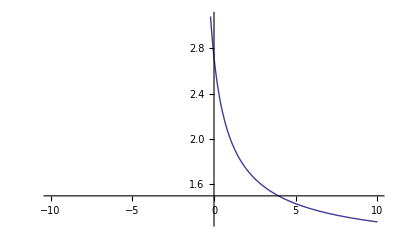

```mathematica
Plot[(1+x)^(1/x),{x,-10,10}]
```

```mathematica
Manipulate[ParametricPlot[{a*Cos[2t],a*Cos[3t]},{t,0,2*π}],{a,2,10}]
```

```mathematica
Manipulate[ParametricPlot[{a/(Cos[t])^3,a*(Tan[t])^3},{t,π/6,π/3}],{a,2,10}]
```

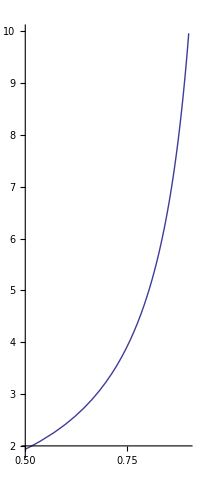

```mathematica
ParametricPlot[{(r-1)/r,(√(r^4-(r-1)^2))/r},{r,2,10}]
```

```mathematica
Manipulate[PolarPlot[(a*Tanh[t])/(t-1),{t,2,50}],{a,2,50}]
```

```mathematica
∫(ArcCot(ⅇ^x)/(ⅇ^x))ⅆx
```

ArcCot x

```mathematica
Integrate[ArcCot[Exp[x]]/(Exp[x]),x]
```

-ⅇ^-x ArcCot[ⅇ^x]+1/2 Log[1+ⅇ^(-2 x)]

```mathematica
Integrate[(x+1)/√(x^2+x+1),x]
```

√(1+x+x^2)+1/2 ArcSinh[(1+2 x)/(√3)]

```mathematica
NSum[((2*n-1)/(2^n)),{n,10}]
```

2.97754

```mathematica
Integrate[Exp[-x^2-y^2]*Cos[x^2+y^2],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

π/2

```mathematica
Integrate[Exp[-x^2-y^2]*Sin[x^2+y^2],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

π/2

```mathematica
A={{-2,8,6},{-4,10,6},{4,-8,-4}}
```

{{-2,8,6},{-4,10,6},{4,-8,-4}}

```mathematica
JordanDecomposition[A]⟦2⟧//MatrixForm
```

(0 | 0 | 0
0 | 2 | 0
0 | 0 | 2)

```mathematica
B={{2,0,1,1,0,0},{1,1,1,0,1,0},{-1,0,0,0,0,1},{0,0,0,2,0,1},{0,0,0,1,1,1},{0,0,0,-1,0,0}}
```

{{2,0,1,1,0,0},{1,1,1,0,1,0},{-1,0,0,0,0,1},{0,0,0,2,0,1},{0,0,0,1,1,1},{0,0,0,-1,0,0}}

```mathematica
JordanDecomposition[B]⟦2⟧//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Apart[(1/(x^4+4))]
```

(2-x)/(8 (2-2 x+x^2))+(2+x)/(8 (2+2 x+x^2))

```mathematica
Apart[x/((x^2-1)^2)]
```

1/(4 (-1+x)^2)-1/(4 (1+x)^2)

```mathematica
Factor[x^5+x^3+x^2+1]
```

(1+x) (1+x^2) (1-x+x^2)

```mathematica
Factor[x^3+2*x^2+4*x+1]
```

1+4 x+2 x^2+x^3

```mathematica
Manipulate[
ParametricPlot[{(R+r)*Cos[t]+r*Cos[t*(R+r)/r],(R+r)*Sin[t]+r*Sin[t*(R+r)/r]},{t,0,2*π}],{r,1,5},{R,7,10}]
```

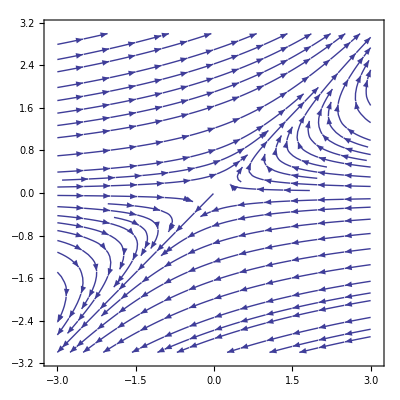

```mathematica
StreamPlot[{-2*x+3y,y},{x,-3,3},{y,-3,3}]
```